```mathematica
<<xlr8r.m
```

xCellerator 0.88 (18-July-2012) loaded 19 July 2012 at 18:27 GMT-06:60 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 1203-002)
GNU General Public License (GPL) Terms Apply.

```mathematica
model={{Overscript[A⇄B, ℰ],k1,k2,k3}};
```

## Species as a parameter is stepped

```mathematica
predictions=PredictTransferFunction[model, {t,0,10}, {k1,0,1,.1}, B, 
initialConditions-> {A-> 1,B->0, ℰ-> 1},
rates-> {k2-> .5, k3-> 1}];
```

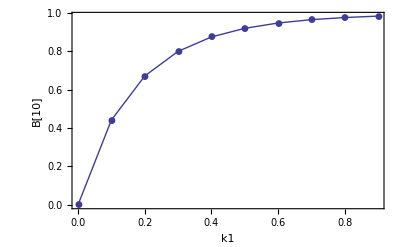

```mathematica
ListPlot[Most[predictions], Joined-> True, PlotMarkers-> Automatic,Frame-> True,  FrameLabel-> {"k1", "B[10]"}]
```

## Species as IC is stepped

```mathematica
predictions=PredictTransferFunction[model, {t,0,10}, {ℰ,0,5,.1}, B, 
initialConditions-> {A-> 1,B->0},
rates-> {k1-> 1, k2-> .5, k3-> 1}];
```

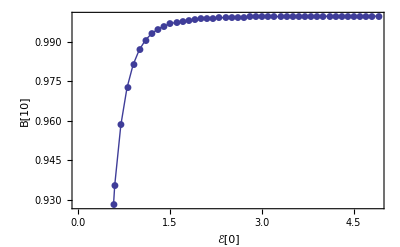

```mathematica
ListPlot[Most[predictions], Joined-> True, PlotMarkers-> Automatic,Frame-> True,  FrameLabel-> {"ℰ[0]", "B[10]"}]
```